# Method of Steepest Descent

A method for finding a local minimum of a differentiable function.

Valeriu Ungureanu, Jun. 24,  2018

The method is known also as the steepest descent method and it includes related algorithms having the same computing scheme based on a gradient concept. The illustrious French mathematician Augustin-Louis Cauchy proposed the method in 1847, much more before the appearing of modern computers. The method is very simple and may be successfully used for computing local minima, generally in combination with other methods as Newton’s method. It has also modifications.

Import an image:

```mathematica
SetDirectory[NotebookDirectory[]];Grid[{{Import["Cauchy.jpg"]},{"Augustin-Louis Cauchy"},{"1789-1857"}}]
```

-Graphics-
Augustin-Louis Cauchy
1789-1857

## A Problem Statement

We consider the problem:

f(x) → min, x∈R^n,

that requires to find an approximation x^k to some local minimum x^* with an accuracy ε>0. The accuracy can refer to:

argument: ||x^k-x^*||<ε_1,

function value: |f(x^k)-f(x^*)|<ε_2,

argument and function value: max{||x^k-x^*||,|f(x^k)-f(x^*)|}<ε_3,

gradient: ||f'(x^k)||<ε_4,

etc.

We have to remark and illustrate that close values of the argument do not guarantee close values of the function:

```mathematica
Manipulate[Column@{1/100,2500(1/10)^2-n,-n,Plot[{(x-1)^2,2500(x-1)^2-n},{x,-1,3},PlotRange->{-31,25},Epilog->{PointSize[Medium],Red,Point[{1,0}],PointSize[Medium],Green,Point[{0.9,0}]}]},{n,0,30,1}]
```

## An Iterative Formula and Ending Conditions

Computations are performed according to the formula:

x^(k+1)=x^k-α_k f'(x^k), k=0,1,2,...

where:

x^0 is the starting point,

f'(x^k) is the gradient of the objective function at x^k,

α_k is the step length on the anti-gradient direction.

Observe that in this formula α_k may be computed differently. For example α_kmay be determined as:

α_k=argmin_(α ≥ 0) f(x^k-α f'(x^k)) - method of optimal steps,

α_k=α λ^s - where: α,λ>0 are fixed numbers,
                                      s ≥ 0 is the least power which ensures f(x^(k+1))<f(x^k) - method of a step fragmentation,

α_k=α>0 - method of constant steps.

Apparently, it looks so that we can now apply the method. But, let us consider the following simple function which doesn’t have optima:

Define a function and plot it:

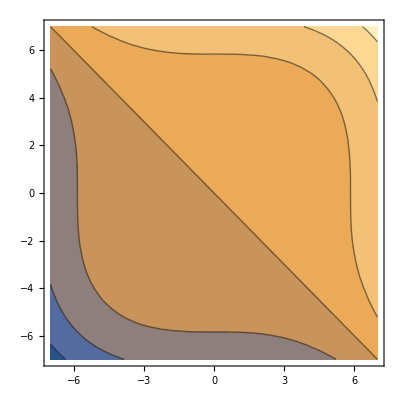
-Graphics3D--Graphics-

```mathematica
f1[{x_,y_}]:=x^3+y^3; Row[{Plot3D[f1[{x,y}],{x,-7,7},{y,-7,7}],ContourPlot[f1[{x,y}],{x,-7,7},{y,-7,7}]}]
```

Evidently, the above algorithm can be applied now. But, it will never stop not only because the function doesn’t have optima. We must define ending conditions:

||x^(k+1)-x^k||<ε_1,

|f(x^(k+1))-f(x^k)|<ε_2,

max{||x^(k+1)-x^k||,|f(x^(k+1))-f(x^k)|}<ε_3,

||f'(x^k)||<ε_4,

etc.

Now, we have ending conditions and we now that it is reasonable to apply algorithm to functions that have local minima. So, let us consider a function that has at least one local minimum.

Define a function and plot it:

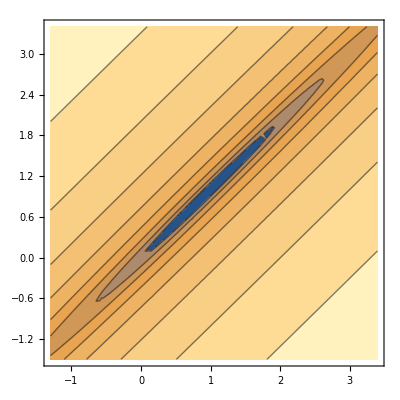
-Graphics3D--Graphics-

```mathematica
f2[{x_,y_}]:=100(y-x)^2+(1-x)^2+0.01; Row[{Plot3D[f2[{x,y}]//Log,{x,-2,4},{y,-2,4}],ContourPlot[f2[{x,y}]//Log,{x,-1.3,3.4},{y,-1.5,3.4}]}]
```

Now, we can present a primitive code of the algorithm:

A procedural cod of the algorithm:

```mathematica
ε=10^-10; Ξ={x,y}; grad[{x_,y_}]=D[f2[Ξ],{Ξ}]; Ξ={-12/10.,1};While[Norm[grad[Ξ]]≥ε , Ξ=Ξ-α grad[Ξ]/.Minimize[{f2[Ξ-α grad[Ξ]],α≤1},α]⟦2⟧];Print[N[Ξ]," ",f2[Ξ]]
```

{1.,1.} 0.01

Remark that the code finds exactly the global minimum point and the global value of the function defined above.

## Computation Monitoring

To understand better the algorithm, let us monitor the computations. There are some known test functions used to verify optimization programs. One of them is the Rosenbrock function:

Define the Rosenbrock function and plot it:

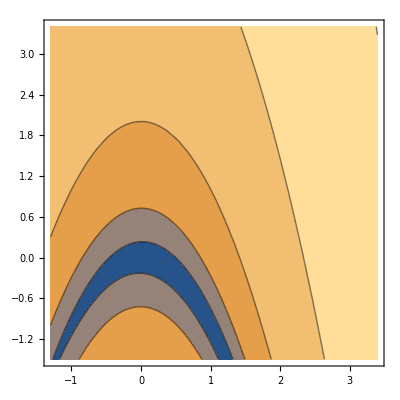
-Graphics3D--Graphics-

```mathematica
f3[{x_,y_}]:=100(-y-x^2)^2+(1-x)^2+1.;Row[{Plot3D[f3[{x,y}]//Log,{x,-2,4},{y,-2,4}],ContourPlot[f3[{x,y}]//Log,{x,-1.3,3.4},{y,-1.5,3.4}]}]
```

For this function we have the following monitoring of computational process:

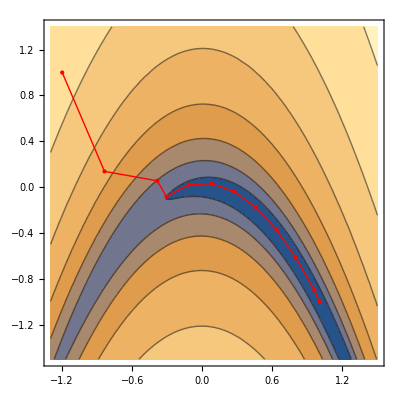

```mathematica
pts = Reap[FindMinimum[f3[{x,y}],{{x,-1.2},{y,1}},StepMonitor:>Sow[{x,y}]]]⟦2,1⟧;pts =Join[{{-1.2,1}},pts];
ContourPlot[f3[{x,y}]//Log,{x,-1.3,1.5},{y,-1.5,1.4},Epilog->{Red,Line[pts],Point[pts]}]
```

We must observe application of the standard Wolfram Mathematica function FindMinimum[]. It finds local minimum of a function. We can try to apply also the precedent code. Unfortunately, it will need much much more time:

```mathematica
ε=10^-1; Ξ={x,y}; grad[{x_,y_}]=D[f3[Ξ],{Ξ}]; Ξ={-12/10.,1};While[Norm[grad[Ξ]]≥ε , Ξ=Ξ-α grad[Ξ]/.Minimize[{f3[Ξ-α grad[Ξ]],α≤1},α]⟦2⟧];Print[N[Ξ]," ",f3[Ξ]]
```

So, we have identified difficulties arising in the application of gradient descent method.

## Test Problems

Application of the gradient method to the optimization of Rosenbrock function highlights some it difficulties. First, we need to know properties of the objective function that guarantee the convergence of the computing process. Second, we need to know what are the requirements for the code which will guarantee a high convergence speed. Wolfram Mathematica has a special package for unconstrained optimization problems.

Load the package:

```mathematica
<<Optimization`UnconstrainedProblems`
```

The package includes 35 test functions:

```mathematica
$FindMinimumProblems
```

{Rosenbrock,FreudensteinRoth,PowellBadlyScaled,BrownBadlyScaled,Beale,JennrichSampson,HelicalValley,Bard,Gauss,Meyer,Gulf,Box3D,PowellSingular,Wood,KowalikOsborne,BrownDennis,Osborne1,BiggsExp6,Osborne2,Watson,ExtendedRosenbrock,ExtendedPowell,PenaltyFunctionI,PenaltyFunctionII,VariablyDimensionedFunction,TrigonometricFunction,BrownAlmostLinear,DiscreteBoundaryValue,DiscreteIntegralEquation,BroydenTridiagonal,BroydenBanded,LinearFullRank,LinearRank1,LinearRank1Z,Chebyquad}

More the more, it includes some useful plotting functions that may be used directly.

Apply the function FindMinimumPlot[]:

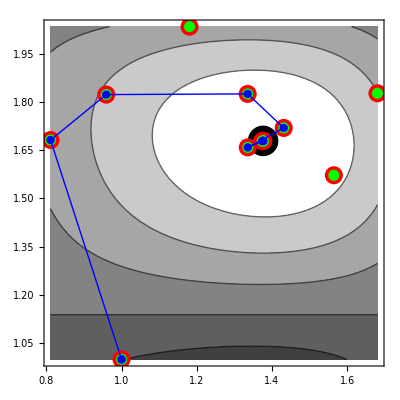
{-2.,{x→1.37638,y→1.67868}}{Steps→9,Function→13,Gradient→13}-Graphics-

```mathematica
FindMinimumPlot[Cos[x^2 - 3 y] + Sin[x^2 + y^2],{{x,1},{y,1}}]//Row
```

Sure, they may be used for the test functions  Optimization`UnconstrainedProblems`paclet:tutorial/UnconstrainedOptimizationTestProblemstoo.

Apply FindMinimumPlot[] to to optimize  the FreudensteinRoth test function:

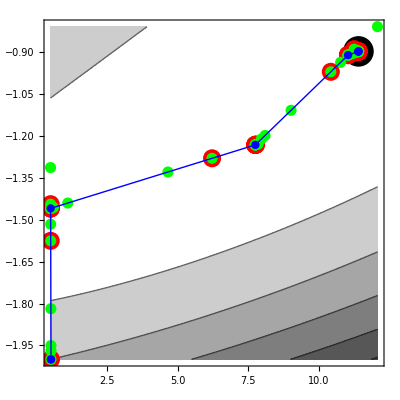
{{48.9843,{X_1→11.4128,X_2→-0.896805}},{Steps→6,Function→56,Gradient→40},-Graphics-}

```mathematica
p1=GetFindMinimumProblem[FreudensteinRoth];FindMinimumPlot[p1, Method->{"Gradient","StepControl"->"TrustRegion"}]
```

So, we highlighted the need to guarantee theoretically the convergence of the computational process.

## Convergence Theorem

This section exposes the convergence theorem and it’s proof. It is not obligatory to read it if you don’t have strong necessity for this.

Theorem.  Let λ∈(0,1).
                        If     f(x) is bounded by bellow,
                                f'(x) satisfies Lipschitz condition for some L>0:
                               ||f'(x)-f'(y)||<L||x-y||, ∀x,y∈R^n, x ≠ y,
                          and  α_k∈(0,(1-λ)/L), ∀k=0,1,2,...,
                than
                          lim_(k→∞) ||f'(x^k)||=0, ∀x^0∈R^n.

Proof.  Let us follow the proof scheme represented with the Wolfram Language function Graph:

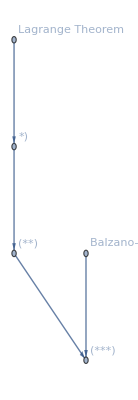

```mathematica
Graph[{Labeled[1,"Lagrange Theorem"],Labeled[2,"*)"],Labeled[3,"(**)"],Labeled[4,"Balzano-Weierstrass Theorem"],Labeled[5,"(***)"]},{1->2,2->3,3->5,4->5}]
```

According to Lagrange theorem there is x∈(x^k,x^(k+1)):

f(x^(k+1))-f(x^k)=(x^(k+1)-x^k)^T f'(x)=
=(x^(k+1)-x^k)^T f'(x^k)+(x^(k+1)-x^k)^T(f'(x)-f'(x^k))≤
≤ -α_k||f'(x^k)(||)^2+α_k||f'(x^k)||L||x-x^k||≤
≤-α_k||f'(x^k)(||)^2+α_kL||f'(x^k)||||x^(k+1)-x^k||=
=α_k||f'(x^k)(||)^2(-1+α_k L).          (*)

If α_k>0 and -1+α_k L<-λ, than

f(x^(k+1))-f(x^k)<-λα_k||f'(x^k)(||)^2<0, for ||f'(x^k)(||)^2≠0.         (**)

That is, for α_k∈(0,(1-λ)/L):

f(x^(k+1))-f(x^k)<0.

As f(x) is bounded by bellow and  {f(x^k)}  decreases, based on Balzano-Weierstrass theorem it follows that:

lim_(k→∞) f(x^(k+1))-f(x^k)=0.

Based on (**) it results the inequality:

||f'(x^k)(||)^2<(f(x^k)-f(x^(k+1)))/λα_k

From the last two expressions:

lim_(k→∞) ||f'(x^k)||=0.  (***)

Q.E.D.

## Conclusions

The method of steepest descent is very simple and convenient to use. Unfortunately, the convergence theorem guarantees  the convergence of the computational process only to stationary points that are not obligatory local minimum points. Nevertheless, the method is successfully used in practice, especially in combination with Newton’s method, for different classes of functions when there are reasons to argue the optimality of the found approximate solution.

Apply FindMinimumPlot[] to to optimize two variable test functions and represent graphically the computation process of the gradient method:

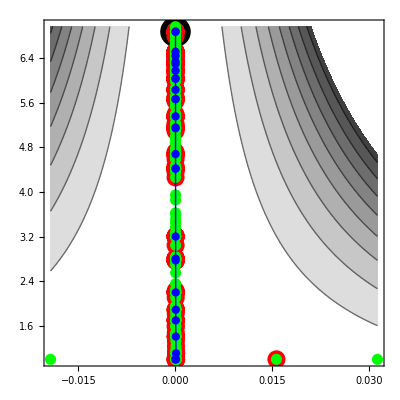
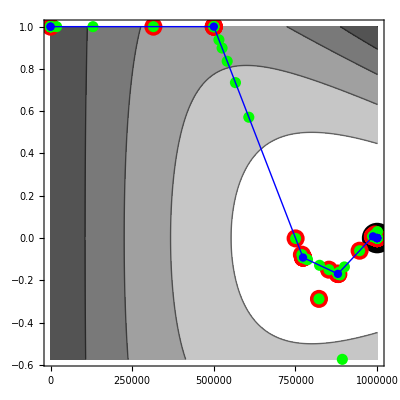
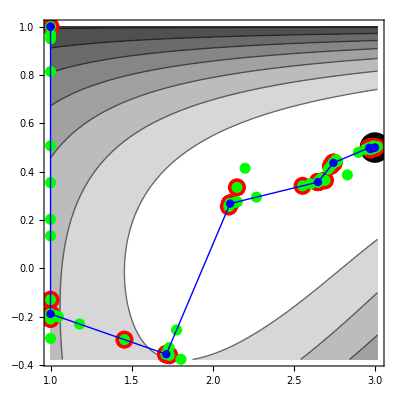
{2.00412×10^-20,{X_1→1.,X_2→1.}} | {Steps→22,Function→247,Gradient→175} | -Graphics-
{48.9843,{X_1→11.4128,X_2→-0.896805}} | {Steps→6,Function→56,Gradient→40} | -Graphics-
{8.49323×10^-7,{X_1→0.0000145493,X_2→6.87295}} | {Steps→27,Function→316,Gradient→219} | -Graphics-
{7.09975×10^-30,{X_1→1.×10^6,X_2→2.×10^-6}} | {Steps→9,Function→87,Gradient→63} | -Graphics-
{9.41622×10^-12,{X_1→3.00001,X_2→0.500002}} | {Steps→9,Function→96,Gradient→64} | -Graphics-
{124.362,{X_1→0.257825,X_2→0.257825}} | {Steps→6,Function→54,Gradient→38} | -Graphics-

```mathematica
FindMinimumPlot[#, Method->{"Gradient","StepControl"->"TrustRegion"}]&/@GetFindMinimumProblem/@$FindMinimumProblems[[1;;6]]//Grid
```

## Further explorations

Conjugate Gradient Method

Newton Method

Coordinate Descent

## Author contact information

v.a.ungureanu@gmail.com

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)